```mathematica
ClearAll
```

ClearAll

```mathematica
logk0=-4;
logkf=1;
step=0.01;
bstep=1;
```

```mathematica
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t];
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t];
η[t_]:=HeavisideTheta[-Log[-t]+7]*0.05-HeavisideTheta[-Log[-t]+3]*0.05;
"η[t_]:=Exp[-(-Log[-t]+5)^2/0.2]*0.05";
"η[t_]:=HeavisideTheta[-Log[-t]+5]*0.05";
"η[t_]:=0.05";
```

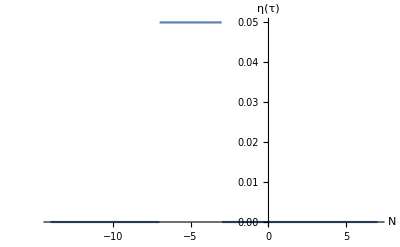

```mathematica
Plot[η[-Exp[-r]],{r,-14, 7},PlotRange->All, AxesLabel->{N,"η(τ)"}]
```

```mathematica
listy1=List[];
listx1=List[];
listy2=List[];
listx2=List[];
listw1=List[];
listv1=List[];
listw2=List[];
listv2=List[];
Plist=List[];
```

```mathematica
listk:=10^Range[logk0,logkf,step];
"listk:=Range[1, 10 ,1]";
listn0:=N@Subdivide[-14,-3,Length[listk]-1];
"listn0:=N@Subdivide[-5,-5,Length[listk]-1]";
listnf :=N@Subdivide[10,10,Length[listk]-1];
"listnf :=N@Subdivide[15,15,Length[listk]-1]";
```

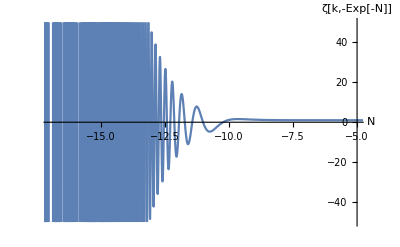

```mathematica
k=listk[[1]];Plot[Re[ζ[-Exp[-r]]],{r,-20,5},PlotRange->{{-17,-5},{-50,50}},AxesLabel->{N, "ζ[k,-Exp[-N]]"}]
```

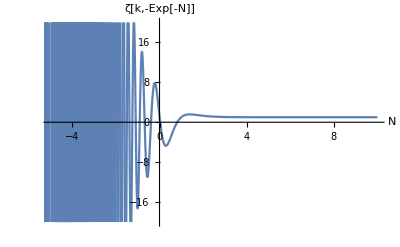

```mathematica
k=listk[[-1]];Plot[Re[ζ[-Exp[-r]]],{r,-10,10},PlotRange->{{-5,10},{-20,20}},AxesLabel->{N, "ζ[k,-Exp[-N]]"}]
```

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s=NDSolve[{
x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*w1[t]+D[cζ[t],t]*cζ[t]*v1[t]), 
y1'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*w1[t]-D[ζ[t],t]*cζ[t]*v1[t]),
w1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]-D[cζ[t],t]*cζ[t]*y1[t]),
v1'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*y1[t]),
x1[-Exp[-n0]]==1, y1[-Exp[-n0]]==0, w1[-Exp[-n0]]==0, v1[-Exp[-n0]]==0},{x1,y1,w1,v1},{t,-Exp[-n0],-Exp[-nf]}],
 yy1[t_]:=y1[t]/.s,AppendTo[listy1,{k,yy1[-Exp[-nf]][[1]]}],
 xx1[t_]:=x1[t]/.s, AppendTo[listx1,{k,xx1[-Exp[-nf]][[1]]}],
ww1[t_]:=w1[t]/.s,AppendTo[listw1,{k,ww1[-Exp[-nf]][[1]]}],
vv1[t_]:=v1[t]/.s,AppendTo[listv1,{k,vv1[-Exp[-nf]][[1]]}] },
{i, 1, Length[listk], 1}]
```

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s2=NDSolve[{
x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*w2[t]+D[cζ[t],t]*cζ[t]*v2[t]), 
y2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*w2[t]-D[ζ[t],t]*cζ[t]*v2[t]),
w2'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x2[t]-D[cζ[t],t]*cζ[t]*y2[t]),
v2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x2[t]+D[cζ[t],t]*ζ[t]*y2[t]), 
x2[-Exp[-n0]]==0, y2[-Exp[-n0]]==0, w2[-Exp[-n0]]==1, v2[-Exp[-n0]]==0},{x2,y2,w2,v2},{t,-Exp[-n0],-Exp[-nf]}], 
yy2[t_]:=y2[t]/.s2,AppendTo[listy2,{k,yy2[-Exp[-nf]][[1]]}],
xx2[t_]:=x2[t]/.s2, AppendTo[listx2,{k,xx2[-Exp[-nf]][[1]]}],
ww2[t_]:=w2[t]/.s2,AppendTo[listw2,{k,ww2[-Exp[-nf]][[1]]}],
vv2[t_]:=v2[t]/.s2,AppendTo[listv2,{k,vv2[-Exp[-nf]][[1]]}]},
 {i, 1, Length[listk], 1}]
```

Gráficos

Power spectrum

```mathematica
Do[AppendTo[Plist,List[listy1[[i]][[1]],(Abs[listy1[[i]][[2]]+listx1[[i]][[2]]])^2+(Abs[listy2[[i]][[2]]+ listx2[[i]][[2]]])^2]],{i,1,Length[listk],1}]
Plist;
```

General::munfl: (6.84007×10^-314)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.73502×10^-314)^2 is too small to represent as a normalized machine number; precision may be lost.

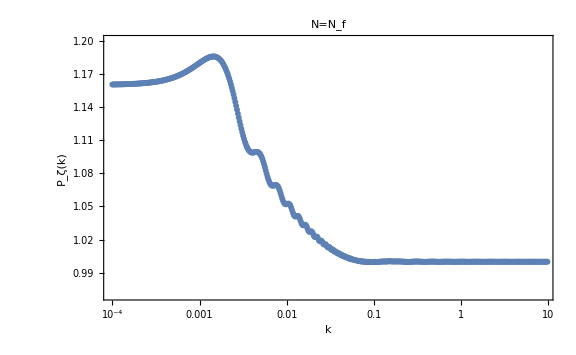

```mathematica
ListLogLinearPlot[Plist, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->{{10^(-4),9},{0.97,1.2}}, Joined->False]
```

Estos próximos 3 plots se utilizan colocando valores de k tal que sean importantes en el gráfico del power spectrum (mínimos y máximos de este)

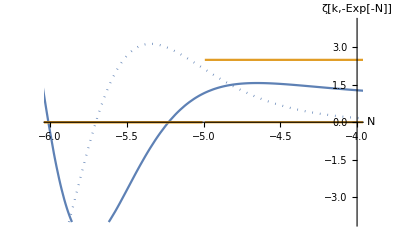

```mathematica
k=0.015;ReImPlot[{ζ[-Exp[-r]],η[-Exp[-r]]*50},{r,-20,5},PlotRange->{{-6,-4},{-4,4}},AxesLabel->{N, "ζ[k,-Exp[-N]]"}]
```

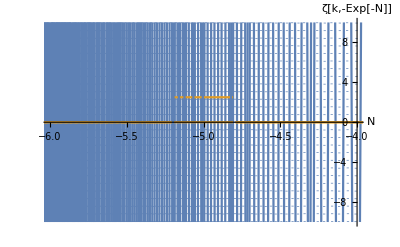

```mathematica
k=1;ReImPlot[{ζ[-Exp[-r]],η[-Exp[-r]]*50},{r,-20,5},PlotRange->{{-6,-4},{-10,10}},AxesLabel->{N, "ζ[k,-Exp[-N]]"}]
```

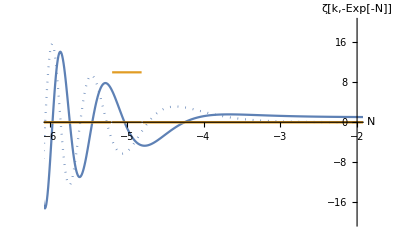

```mathematica
k=0.04;ReImPlot[{ζ[-Exp[-r]],η[-Exp[-r]]*200},{r,-20,5},PlotRange->{{-6,-2},{-20,20}},AxesLabel->{N, "ζ[k,-Exp[-N]]"}]
```

Coeficientes Bogoliubov primer modo

```mathematica
listx1R := List[];
listx1I := List[];
Do[AppendTo[listx1R,List[listx1[[i]][[1]],Re[listx1[[i]][[2]]]]],{i,1,Length[listx1],1}];
Do[AppendTo[listx1I,List[listx1[[i]][[1]],Im[listx1[[i]][[2]]]]],{i,1,Length[listx1],1}];
```

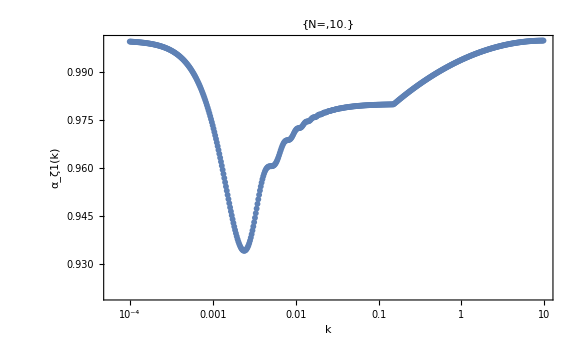

```mathematica
ListLogLinearPlot[{listx1R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style[{"N=",listnf[[1]]}, Black, FontSize->20], PlotRange->Automatic]
```

```mathematica
listy1R := List[];
listy1I := List[];
Do[AppendTo[listy1R,List[listy1[[i]][[1]],Re[listy1[[i]][[2]]]]],{i,1,Length[listy1],1}];
Do[AppendTo[listy1I,List[listy1[[i]][[1]],Im[listy1[[i]][[2]]]]],{i,1,Length[listy1],1}];
```

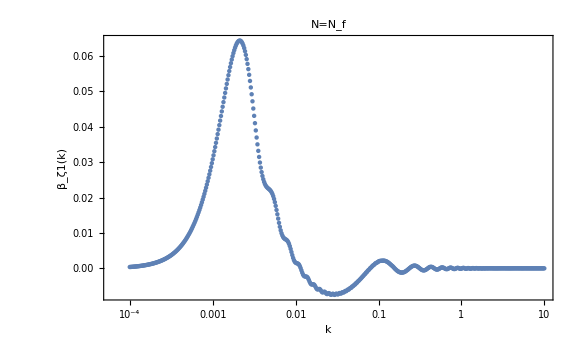

```mathematica
ListLogLinearPlot[{listy1R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->Automatic]
```

```mathematica
listw1R := List[];
listw1I := List[];
Do[AppendTo[listw1R,List[listw1[[i]][[1]],Re[listw1[[i]][[2]]]]],{i,1,Length[listw1],1}];
Do[AppendTo[listw1I,List[listw1[[i]][[1]],Im[listw1[[i]][[2]]]]],{i,1,Length[listw1],1}];
```

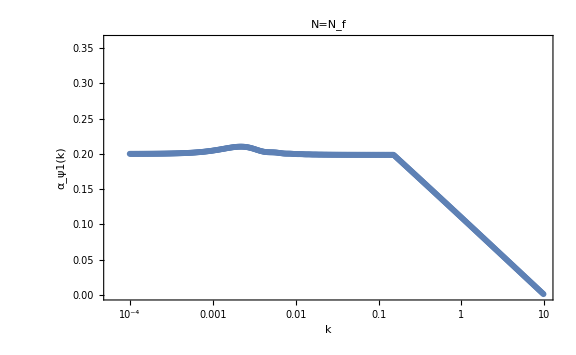

```mathematica
ListLogLinearPlot[{listw1R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ψ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->Automatic]
```

```mathematica
listv1R := List[];
listv1I := List[];
Do[AppendTo[listv1R,List[listv1[[i]][[1]],Re[listv1[[i]][[2]]]]],{i,1,Length[listv1],1}];
Do[AppendTo[listv1I,List[listv1[[i]][[1]],Im[listv1[[i]][[2]]]]],{i,1,Length[listv1],1}];
```

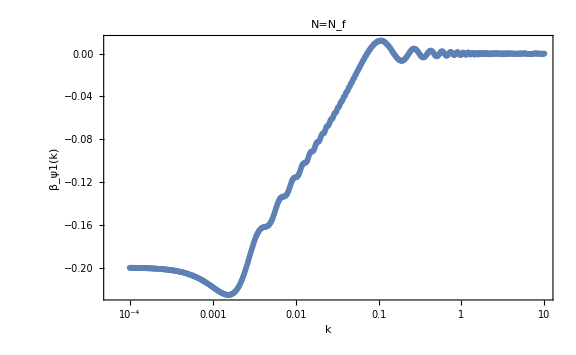

```mathematica
ListLogLinearPlot[{listv1R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ψ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->Automatic]
```

Coeficientes Bogoliubov segundo modo

```mathematica
listx2R := List[];
listx2I := List[];
Do[AppendTo[listx2R,List[listx2[[i]][[1]],Re[listx2[[i]][[2]]]]],{i,1,Length[listx2],1}];
Do[AppendTo[listx2I,List[listx2[[i]][[1]],Im[listx2[[i]][[2]]]]],{i,1,Length[listx2],1}];
```

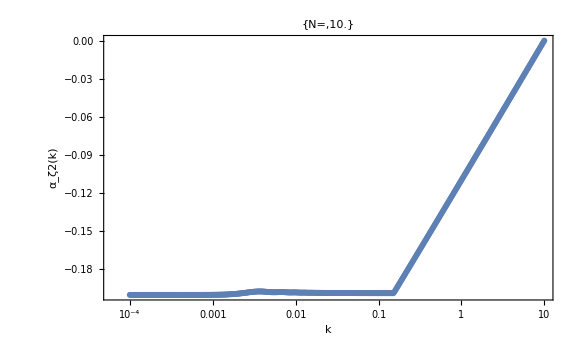

```mathematica
ListLogLinearPlot[{listx2R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style[{"N=",listnf[[1]]}, Black, FontSize->20], PlotRange->Automatic]
```

```mathematica
listy2R := List[];
listy2I := List[];
Do[AppendTo[listy2R,List[listy2[[i]][[1]],Re[listy2[[i]][[2]]]]],{i,1,Length[listy2],1}];
Do[AppendTo[listy2I,List[listy2[[i]][[1]],Im[listy2[[i]][[2]]]]],{i,1,Length[listy2],1}];
```

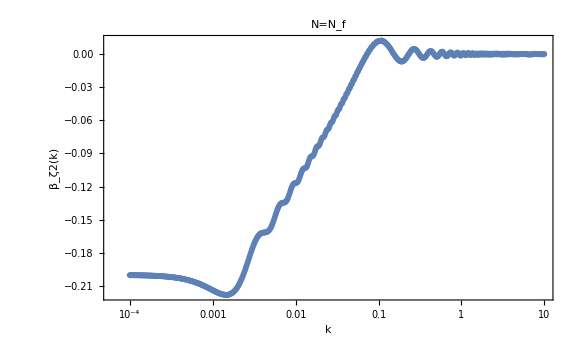

```mathematica
ListLogLinearPlot[{listy2R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->All]
```

```mathematica
listw2R := List[];
listw2I := List[];
Do[AppendTo[listw2R,List[listw2[[i]][[1]],Re[listw2[[i]][[2]]]]],{i,1,Length[listw2],1}];
Do[AppendTo[listw2I,List[listw2[[i]][[1]],Im[listw2[[i]][[2]]]]],{i,1,Length[listw2],1}];
```

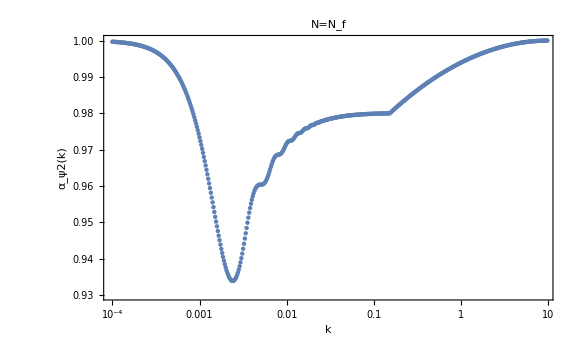

```mathematica
ListLogLinearPlot[{listw2R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ψ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->Automatic]
```

```mathematica
listv2R := List[];
listv2I := List[];
Do[AppendTo[listv2R,List[listv2[[i]][[1]],Re[listv2[[i]][[2]]]]],{i,1,Length[listv2],1}];
Do[AppendTo[listv2I,List[listv2[[i]][[1]],Im[listv2[[i]][[2]]]]],{i,1,Length[listv2],1}];
```

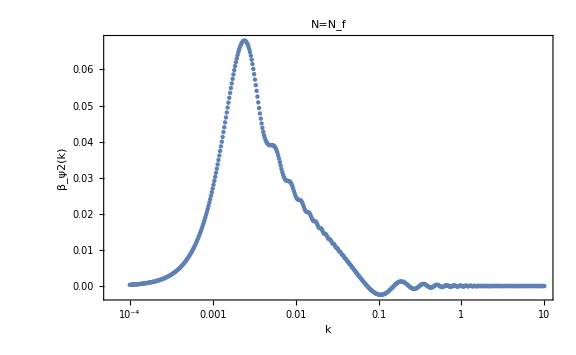

```mathematica
ListLogLinearPlot[{listv2R}, PlotStyle->Dashed, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ψ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N=N_f", Black, FontSize->20], PlotRange->Automatic]
```